# LifeWiki Dataset 2025

An updated and cleaned dataset sourced from the game of life wiki website

### Details

The LifeWiki Dataset 2025 contains information extracted from the LifeWiki, the most comprehensive online resource for Conway's Game of Life. This dataset has been meticulously cleaned and formatted for use in computational analysis, pattern discovery, and historical research in cellular automata.

"Name" | The name of the pattern
"Year" | The year the pattern was first discovered
"MatrixData" | The initial pattern in the form of a 2D Sparse Array
"Class" | The type of pattern, potential classes include "Oscillator", "Strict still life", "Spaceship" and more
"InitialWeight" | The number of black cells in the initial array
"Wiki" | URL to the wiki page for this particular pattern
"DataFiles" | Name of files on the LifeWiki website. Use the link https://conwaylife.com/patterns/[DataFile] to view the file
"Speed" | For gliders and spaceships, this gives the distance the object moves per step

## Data Definitions

### Primary Content

```mathematica
raw = Import[CloudObject["https://www.wolframcloud.com/obj/sw-writings/$LifeData"]];
```

```mathematica
mainkeys ={"Name","Year","Class","Period","Wiki","DataFiles","MatrixData","InitialWeight", "Speed"};
```

```mathematica
ld =ReplacePart[raw, Key["Chucklebait"]-> Merge[{raw["Chucklebait"], <|"Class"->"Strict still life"|>},Last]];
```

```mathematica
sas = ;
```

```mathematica
urls = {"https://conwaylife.com/wiki/Period-20_glider_gun","https://conwaylife.com/wiki/Period-40_glider_gun","https://conwaylife.com/wiki/P21_B-heptomino_hassler#Guns","https://conwaylife.com/wiki/58P37","https://conwaylife.com/wiki/Period-16_glider_gun", "https://conwaylife.com/wiki/Period-15_glider_gun", "https://conwaylife.com/wiki/Period-47_glider_gun", "https://conwaylife.com/wiki/Period-35_glider_gun"};
```

```mathematica
names={"Period-20 glider gun","Period-40 glider gun","P21 B-heptomino hassler","58P37","Period-16 glider gun","Period-15 glider gun","Period-47 glider gun","Period-35 glider gun"};
```

```mathematica
ggs = Association[MapThread[#1->Join[<|"Name"->#1, "Wiki"-> #2, "InitialWeight"->#3["MatrixData"]["ExplicitLength"], "Class"->"Gun"|>, #3]&, {names, urls, SortBy[sas, #Year&]}]];
```

```mathematica
ld = Append[ld, ggs];
```

```mathematica
n1 = "p12rpentominohassler-01"-><|"Name"->"p12rpentominohassler-01","Year"->1995,"Class"->"Oscillator","Period"->12,"Wiki"->"https://conwaylife.com/wiki/R-pentomino_hasslers","DataFiles"->{"p12rpentominohasslers.rle"},"MatrixData"->SparseArray[…],"InitialWeight"->315,"Speed"->Missing["NotApplicable"]|>;
```

```mathematica
n2 = "p12rpentominohassler-02"-><|"Name"->"p12rpentominohassler-02","Year"->1995,"Class"->"Oscillator","Period"->12,"Wiki"->"https://conwaylife.com/wiki/R-pentomino_hasslers","DataFiles"->{"p12rpentominohasslers.rle"},"MatrixData"->SparseArray[…],"InitialWeight"->315,"Speed"->Missing["NotApplicable"]|>;
```

```mathematica
filled = AssociationThread[mainkeys, Lookup[#, mainkeys, Missing["NotApplicable"]]]&/@ld;
```

```mathematica
AppendTo[filled, #]&/@ {n1, n2};
```

```mathematica
filled = Delete[filled, Key["p12rpentominohasslers"]];
```

```mathematica
ResourceData[{{}}]=filled;
```

### Additional Data Elements (optional)

## Examples

### Basic Examples

```mathematica
Dataset[ResourceData[{{}}]["Gosper glider gun"]]
```

-Graphics-

### Scope & Additional Elements

Group by class:

```mathematica
Dataset[GroupBy[Values[ResourceData[{{}}]], #Class&->({#Name, #Year}&)]]
```

-Graphics-

List the first five spaceships ever discovered:

```mathematica
Dataset[{ArrayPlot[#MatrixData], #Year}&/@TakeSmallestBy[Select[ResourceData[{{}}], #Class === "Spaceship"&],#Year&,  5]]
```

-Graphics-

### Visualizations

See the pattern:

```mathematica
ArrayPlot[ResourceData[{{}}]["Gosper glider gun", "MatrixData"]]
```

-Graphics-

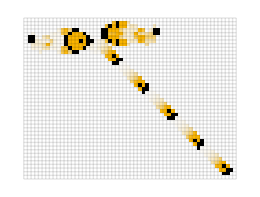

```mathematica
Options[CellularAutomatonHistoryPlot] = {Mesh->True, MeshStyle->Opacity[.1],ColorRules->{-1->Black, x_/; x!=-1:>Blend[RGBColor/@{Hue[0., 0., 1.],Hue[0.12, 0.43, 0.98],Hue[0.12, 1, 0.99]},x]}, "Decay"-> .8, "Margin"-> 1};
CellularAutomatonHistoryPlot[rule_,init_,t_,opts___]:=
Module[{allops = Merge[{Options[CellularAutomatonHistoryPlot],opts},Last]},
ArrayPlot[
With[{u=
ArrayPad[#, allops["Margin"]]&/@CellularAutomaton[rule,init,t]},MapThread[If[#2==1,-1,#]&,{Fold[allops["Decay"] #+#2&,u],Last[u]},2]],Sequence@@FilterRules[Normal@allops, Options[ArrayPlot]]]]
CellularAutomatonHistoryPlot["GameOfLife",{ResourceData[{{}}]["Gosper glider gun"]["MatrixData"], 0},150,ImageSize->260]
```

```mathematica
CellularAutomatonPlot3D[rule_,init_,t_,opts___]:=ArrayPlot3D[
CellularAutomaton[rule,init,t],opts,
  ColorFunction->(If[#==1,SetAlphaChannel[ RGBColor[1., 0.6436, 0.03622],1],Transparent] &),
  ColorFunctionScaling->False,ImageSize->500,Mesh->None,MeshStyle->Opacity[.3]]
CellularAutomatonPlot3D["GameOfLife",{ResourceData[{{}}]["Gosper glider gun"]["MatrixData"], 0},100,ImageSize->140,ViewPoint->{-2.198487002413733,-2.3413385931086927,1.0652645176845457}]
```

-Graphics3D-

```mathematica
CellularAutomatonSpacetimePlot[rule_,init_,t_,opts___]:=
Module[{allops = Merge[{Mesh->True, MeshStyle->Opacity[.1],ColorRules->{-1->Black, x_/; x!=-1:>Blend[RGBColor/@{Hue[0., 0., 1.],Hue[0.12, 0.43, 0.98],Hue[0.12, 1, 0.99]},x]},opts},Last]},
ArrayPlot[With[{u=Transpose@CellularAutomaton[rule,init,t]},
MapThread[If[#2==1,-1,#]&,{Fold[allops["Decay"] #+#2&,u],Last[u]},2]],Sequence@@FilterRules[Normal@allops, Options[ArrayPlot]]]]
CellularAutomatonSpacetimePlot["GameOfLife",{ResourceData[{{}}]["Gosper glider gun"]["MatrixData"], 0},150,"Decay"->.99,ImageSize->95,Mesh->None]
```

-Graphics-

See the accumulation of discoveries in different classes over time:

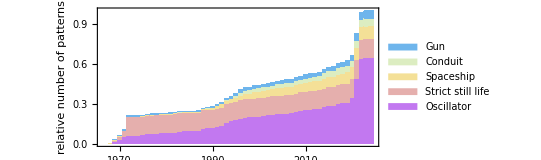

```mathematica
Module[{topclasses = Keys[TakeLargest[CountsBy[Values[ResourceData[{{}}]], #Class&], 5]]},
vals = Accumulate[#] / Total[#, 2]&[Table[Lookup[#, i, Table[0, 5]]&[
Lookup[CountsBy[#, #Class&], topclasses, 0]&/@GroupBy[Values[ResourceData[{{}}]], #Year&]],
 {i, 1969, 2025}]] ;
BarChart[vals,ChartLayout->"Stacked", ChartStyle->"Pastel", FrameTicks->{Automatic, {Table[{i, i + 1967},{i, 3, 57, 10}], Automatic}}, Frame->True,ChartLegends->topclasses, FrameLabel->{None, "relative number of patterns"}, AspectRatio->.4]
]
```

View the size and number of discoveries by decade:

```mathematica
Module[{}, bw = ReverseSortBy[#, #InitialWeight&]&/@GroupBy[Values[ResourceData[{{}}]], Round[#Year, 10]&];
bubs = MapIndexed[{#2[[1, 1]], #2[[2]], #InitialWeight}&, bw, {2}];
BubbleChart[Values[bubs], ChartElements->Graphics[Rectangle[]], FrameLabel->{None, "number of patterns"}, AspectRatio->.4]]
```

-Graphics-

See the decreases in different periods over time:

```mathematica
byp=SortBy[(SortBy[#,#Year&]&/@GatherBy[Values[Select[ResourceData[{{}}],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&&1<=#[["Period"]]<60&]],#Period&]),#[[1,"Period"]]&];
allis =Discard[DeleteDuplicates[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],#]]&/@byp, Length[#] ==1&];
ListLinePlot[MapIndexed[{#Year, Times@@Dimensions[#MatrixData]}&, allis, {2}],  ScalingFunctions->"Log", Mesh->All,Frame->True, FrameLabel->{None, "Size of pattern"}, AspectRatio->.4]
```

-Graphics-

Frequency as a function of size:

```mathematica
iws = ReverseSort[CountsBy[Values[ResourceData[{{}}]], #InitialWeight&]];
ListLogLogPlot[iws, PlotRange->All, Frame->True, FrameLabel->{"frequency", "size"}, AspectRatio->.4]
```

-Graphics-

## Source & Additional Information

### Submitted By

Willem Nielsen, Ed Pegg, Stephen Wolfram

### Source/Reference Citation

LifeWiki

### Detailed Source Information

#### Author/Creator

Author Name

#### Source Title

Published Title

#### Source Date

Original Publication Date

#### Source Publisher

Original Publication

#### Geographic Coverage

Area

#### Temporal Coverage

Timespan

#### Source Language

Language

#### Rights

Data Rights

### Links

LifeWiki

### Keywords

Game of life

Cellular Automaton

Conway

### Categories

Agriculture
 Computer Systems
 Economics
 Geometry Data
 Healthcare
 Language
 Mathematics
 Politics
 Statistics |  Astronomy
 Culture
 Education
 Government
 History
 Life Science
 Medicine
 Reference
 Text & Literature |  Chemistry
 Demographics
 Engineering
 Graphics
 Human Activities
 Machine Learning
 Meteorology
 Social Media
 Transportation |  Computational Universe
 Earth Science
 Geography
 Health
 Images
 Manufacturing
 Physical Sciences
 Sociology

### Content Types

Audio
 Image
 Vector Database |  Entity Store
 Numerical Data
 Video |  Geospatial Data
 Text
 |  Graphs
 Time Series

### Related Resource Objects

### Related Symbols

## Author Notes

## Submission Notes